```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[10],Join[Table[{i,i-1},{i,Range[2,10,1]}],Table[{i,i+1},{i,Range[1,10,1]}]]->-t]
```

```mathematica
T[t_]:=T[t]=t*IdentityMatrix[10]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,1,0]],A:=Inverse[β[ω,δ,1,0]],T:=T[1]},Do[J=Inverse[IdentityMatrix[10]-A.T.J.T].A,150000];J=J]
```

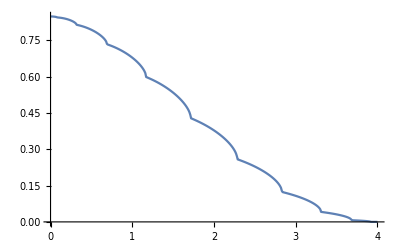

```mathematica
ListLinePlot[Table[{ω,-Im[LEFT[ω,0.0001,1,0]][[1,1]]},{ω,Range[0,4,0.01]}]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[10]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[10]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[10]-SL[ω,δ,1,0].T[1].SR[ω,δ,1,0].T[1]].SL[ω,δ,1,0]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[10]-SR[ω,δ,1,0].T[1].SL[ω,δ,1,0].T[1]].SR[ω,δ,1,0]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,1,0].T[1].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T[1].grr[ω,δ,t,ϵ].T[1]-T[1].GNON[ω,δ,t,ϵ].T[1].GNON[ω,δ,t,ϵ]]
```

```mathematica
pris=Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[0,4,0.01]}]
```

{{0.,10.},{0.01,10.},{0.02,10.},{0.03,10.},{0.04,10.},{0.05,10.},{0.06,9.99999},{0.07,9.99998},{0.08,9.99758},{0.09,9.00003},{0.1,9.00001},{0.11,9.},{0.12,9.},{0.13,9.},{0.14,9.},{0.15,9.},{0.16,9.},{0.17,9.},{0.18,9.},{0.19,9.},{0.2,9.},{0.21,9.},{0.22,9.},{0.23,9.},{0.24,9.},{0.25,9.},{0.26,9.},{0.27,9.},{0.28,9.},{0.29,9.},{0.3,8.99999},{0.31,8.99996},{0.32,8.0004},{0.33,8.00002},{0.34,8.},{0.35,8.},{0.36,8.},{0.37,8.},{0.38,8.},{0.39,8.},{0.4,8.},{0.41,8.},{0.42,8.},{0.43,8.},{0.44,8.},{0.45,8.},{0.46,8.},{0.47,8.},{0.48,8.},{0.49,8.},{0.5,8.},{0.51,8.},{0.52,8.},{0.53,8.},{0.54,8.},{0.55,8.},{0.56,8.},{0.57,8.},{0.58,8.},{0.59,8.},{0.6,8.},{0.61,8.},{0.62,8.},{0.63,8.},{0.64,8.},{0.65,8.},{0.66,8.},{0.67,7.99999},{0.68,7.99998},{0.69,7.97059},{0.7,7.00003},{0.71,7.00001},{0.72,7.},{0.73,7.},{0.74,7.},{0.75,7.},{0.76,7.},{0.77,7.},{0.78,7.},{0.79,7.},{0.8,7.},{0.81,7.},{0.82,7.},{0.83,7.},{0.84,7.},{0.85,7.},{0.86,7.},{0.87,7.},{0.88,7.},{0.89,7.},{0.9,7.},{0.91,7.},{0.92,7.},{0.93,7.},{0.94,7.},{0.95,7.},{0.96,7.},{0.97,7.},{0.98,7.},{0.99,7.},{1.,7.},{1.01,7.},{1.02,7.},{1.03,7.},{1.04,7.},{1.05,7.},{1.06,7.},{1.07,7.},{1.08,7.},{1.09,7.},{1.1,7.},{1.11,7.},{1.12,7.},{1.13,7.},{1.14,7.},{1.15,6.99999},{1.16,6.99997},{1.17,6.00359},{1.18,6.00002},{1.19,6.00001},{1.2,6.},{1.21,6.},{1.22,6.},{1.23,6.},{1.24,6.},{1.25,6.},{1.26,6.},{1.27,6.},{1.28,6.},{1.29,6.},{1.3,6.},{1.31,6.},{1.32,6.},{1.33,6.},{1.34,6.},{1.35,6.},{1.36,6.},{1.37,6.},{1.38,6.},{1.39,6.},{1.4,6.},{1.41,6.},{1.42,6.},{1.43,6.},{1.44,6.},{1.45,6.},{1.46,6.},{1.47,6.},{1.48,6.},{1.49,6.},{1.5,6.},{1.51,6.},{1.52,6.},{1.53,6.},{1.54,6.},{1.55,6.},{1.56,6.},{1.57,6.},{1.58,6.},{1.59,6.},{1.6,6.},{1.61,6.},{1.62,6.},{1.63,6.},{1.64,6.},{1.65,6.},{1.66,6.},{1.67,6.},{1.68,6.},{1.69,6.},{1.7,5.99999},{1.71,5.99991},{1.72,5.00012},{1.73,5.00001},{1.74,5.},{1.75,5.},{1.76,5.},{1.77,5.},{1.78,5.},{1.79,5.},{1.8,5.},{1.81,5.},{1.82,5.},{1.83,5.},{1.84,5.},{1.85,5.},{1.86,5.},{1.87,5.},{1.88,5.},{1.89,5.},{1.9,5.},{1.91,5.},{1.92,5.},{1.93,5.},{1.94,5.},{1.95,5.},{1.96,5.},{1.97,5.},{1.98,5.},{1.99,5.},{2.,5.},{2.01,5.},{2.02,5.},{2.03,5.},{2.04,5.},{2.05,5.},{2.06,5.},{2.07,5.},{2.08,5.},{2.09,5.},{2.1,5.},{2.11,5.},{2.12,5.},{2.13,5.},{2.14,5.},{2.15,5.},{2.16,5.},{2.17,5.},{2.18,5.},{2.19,5.},{2.2,5.},{2.21,5.},{2.22,5.},{2.23,5.},{2.24,5.},{2.25,5.},{2.26,5.},{2.27,4.99999},{2.28,4.99988},{2.29,4.00009},{2.3,4.00001},{2.31,4.},{2.32,4.},{2.33,4.},{2.34,4.},{2.35,4.},{2.36,4.},{2.37,4.},{2.38,4.},{2.39,4.},{2.4,4.},{2.41,4.},{2.42,4.},{2.43,4.},{2.44,4.},{2.45,4.},{2.46,4.},{2.47,4.},{2.48,4.},{2.49,4.},{2.5,4.},{2.51,4.},{2.52,4.},{2.53,4.},{2.54,4.},{2.55,4.},{2.56,4.},{2.57,4.},{2.58,4.},{2.59,4.},{2.6,4.},{2.61,4.},{2.62,4.},{2.63,4.},{2.64,4.},{2.65,4.},{2.66,4.},{2.67,4.},{2.68,4.},{2.69,4.},{2.7,4.},{2.71,4.},{2.72,4.},{2.73,4.},{2.74,4.},{2.75,4.},{2.76,4.},{2.77,4.},{2.78,4.},{2.79,4.},{2.8,4.},{2.81,3.99999},{2.82,3.99998},{2.83,3.99641},{2.84,3.00003},{2.85,3.00001},{2.86,3.},{2.87,3.},{2.88,3.},{2.89,3.},{2.9,3.},{2.91,3.},{2.92,3.},{2.93,3.},{2.94,3.},{2.95,3.},{2.96,3.},{2.97,3.},{2.98,3.},{2.99,3.},{3.,3.},{3.01,3.},{3.02,3.},{3.03,3.},{3.04,3.},{3.05,3.},{3.06,3.},{3.07,3.},{3.08,3.},{3.09,3.},{3.1,3.},{3.11,3.},{3.12,3.},{3.13,3.},{3.14,3.},{3.15,3.},{3.16,3.},{3.17,3.},{3.18,3.},{3.19,3.},{3.2,3.},{3.21,3.},{3.22,3.},{3.23,3.},{3.24,3.},{3.25,3.},{3.26,3.},{3.27,3.},{3.28,3.},{3.29,2.99999},{3.3,2.99997},{3.31,2.02941},{3.32,2.00002},{3.33,2.00001},{3.34,2.},{3.35,2.},{3.36,2.},{3.37,2.},{3.38,2.},{3.39,2.},{3.4,2.},{3.41,2.},{3.42,2.},{3.43,2.},{3.44,2.},{3.45,2.},{3.46,2.},{3.47,2.},{3.48,2.},{3.49,2.},{3.5,2.},{3.51,2.},{3.52,2.},{3.53,2.},{3.54,2.},{3.55,2.},{3.56,2.},{3.57,2.},{3.58,2.},{3.59,2.},{3.6,2.},{3.61,2.},{3.62,2.},{3.63,2.},{3.64,2.},{3.65,2.},{3.66,1.99999},{3.67,1.99998},{3.68,1.9996},{3.69,1.00004},{3.7,1.00001},{3.71,1.},{3.72,1.},{3.73,1.},{3.74,1.},{3.75,1.},{3.76,1.},{3.77,1.},{3.78,1.},{3.79,1.},{3.8,1.},{3.81,1.},{3.82,1.},{3.83,1.},{3.84,1.},{3.85,1.},{3.86,0.999999},{3.87,0.999999},{3.88,0.999998},{3.89,0.999997},{3.9,0.999993},{3.91,0.999969},{3.92,0.00241242},{3.93,0.0000205375},{3.94,5.64241×10^-6},{3.95,2.59662×10^-6},{3.96,1.49105×10^-6},{3.97,9.69224×10^-7},{3.98,6.8212×10^-7},{3.99,5.07345×10^-7},{4.,3.9301×10^-7}}

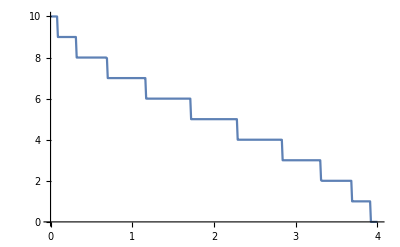

```mathematica
ListPlot[pris,Joined->True]
```

```mathematica
deltae[ω_,ϵ1_]:=Module[{Tin=T[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];tra:= Module[{},list={RandomSample[{imp7,imp10,imp9,imp,imp1,imp,imp,imp,imp9,imp9,imp5,imp,imp8,imp11,imp13,imp,imp3,imp3,imp,imp,imp14,imp,imp13,imp8,imp,imp11,imp,imp8,imp7,imp,imp,imp,imp5,imp,imp,imp14,imp,imp5,imp10,imp,imp10,imp2,imp6,imp,imp2,imp11,imp,imp6,imp4,imp,imp,imp,imp,imp6,imp,imp,imp,imp4,imp1,imp,imp10,imp,imp2,imp13,imp,imp4,imp14,imp7,imp,imp11,imp8,imp4,imp7,imp,imp12,imp,imp,imp12,imp14,imp,imp,imp3,imp5,imp,imp1,imp,imp,imp12,imp13,imp2,imp1,imp,imp6,imp12,imp,imp3,imp9,imp,imp,imp}]};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[10]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[10]-sl1.Tin.SR[ω,0.0001,1,0].Tin].sl1;
Ir1:=Inverse[IdentityMatrix[10]-SR[ω,0.0001,1,0].Tin.sl1.Tin].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].Tin.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]>10,10,Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]]];
b];
tra]
```

```mathematica
Mean[Table[deltae[0,0.5],25000]]
```

2.1383

```mathematica
Mean[Table[deltae[0,0.5],25000]]
```

2.12079

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.5],25000]]},{ω,Range[0,4,0.01]}]
```

{{0.,2.13929},{0.01,2.25582},{0.02,2.2703},{0.03,2.14196},{0.04,2.07515},{0.05,2.15624},{0.06,2.52896},{0.07,3.82821},{0.08,8.16817},{0.09,6.7737},{0.1,4.28157},{0.11,3.05898},{0.12,3.00962},{0.13,3.3853},{0.14,3.70709},{0.15,3.87608},{0.16,4.00078},{0.17,4.0713},{0.18,4.09674},{0.19,4.10183},{0.2,4.10299},{0.21,4.05651},{0.22,3.96475},{0.23,3.88903},{0.24,3.75627},{0.25,3.60258},{0.26,3.38605},{0.27,3.12987},{0.28,2.75217},{0.29,2.29715},{0.3,1.83163},{0.31,2.33686},{0.32,6.9704},{0.33,4.77824},{0.34,3.45504},{0.35,3.47376},{0.36,4.00662},{0.37,4.44796},{0.38,4.70974},{0.39,4.86148},{0.4,4.96738},{0.41,5.02191},{0.42,5.06228},{0.43,5.08824},{0.44,5.1082},{0.45,5.11641},{0.46,5.12014},{0.47,5.11516},{0.48,5.10752},{0.49,5.09775},{0.5,5.08601},{0.51,5.06729},{0.52,5.04294},{0.53,5.01757},{0.54,4.98172},{0.55,4.9326},{0.56,4.88855},{0.57,4.83692},{0.58,4.77486},{0.59,4.69756},{0.6,4.60174},{0.61,4.48118},{0.62,4.34182},{0.63,4.18997},{0.64,3.95845},{0.65,3.65746},{0.66,3.24755},{0.67,2.62889},{0.68,1.77257},{0.69,5.57547},{0.7,4.4052},{0.71,3.48247},{0.72,3.48711},{0.73,4.05212},{0.74,4.50735},{0.75,4.77376},{0.76,4.90698},{0.77,4.98388},{0.78,5.04134},{0.79,5.07227},{0.8,5.10071},{0.81,5.12056},{0.82,5.12896},{0.83,5.14303},{0.84,5.13885},{0.85,5.14487},{0.86,5.14586},{0.87,5.14282},{0.88,5.13843},{0.89,5.13241},{0.9,5.12368},{0.91,5.11885},{0.92,5.10462},{0.93,5.0926},{0.94,5.07533},{0.95,5.06042},{0.96,5.0429},{0.97,5.01676},{0.98,4.99884},{0.99,4.96962},{1.,4.94682},{1.01,4.90823},{1.02,4.87116},{1.03,4.82891},{1.04,4.78413},{1.05,4.73958},{1.06,4.6739},{1.07,4.61369},{1.08,4.5254},{1.09,4.43205},{1.1,4.32571},{1.11,4.17525},{1.12,4.00024},{1.13,3.74862},{1.14,3.40051},{1.15,2.84976},{1.16,1.89425},{1.17,5.14794},{1.18,3.70796},{1.19,3.09946},{1.2,3.29652},{1.21,3.89278},{1.22,4.28747},{1.23,4.47818},{1.24,4.575},{1.25,4.62571},{1.26,4.66321},{1.27,4.68616},{1.28,4.7013},{1.29,4.71509},{1.3,4.71962},{1.31,4.72669},{1.32,4.72752},{1.33,4.73186},{1.34,4.72946},{1.35,4.72531},{1.36,4.72571},{1.37,4.71851},{1.38,4.71678},{1.39,4.71012},{1.4,4.70728},{1.41,4.70194},{1.42,4.6915},{1.43,4.68078},{1.44,4.67227},{1.45,4.66226},{1.46,4.65076},{1.47,4.63726},{1.48,4.62561},{1.49,4.60854},{1.5,4.59366},{1.51,4.57764},{1.52,4.55665},{1.53,4.53837},{1.54,4.5075},{1.55,4.48022},{1.56,4.45567},{1.57,4.42258},{1.58,4.38063},{1.59,4.34833},{1.6,4.30208},{1.61,4.24307},{1.62,4.18598},{1.63,4.1207},{1.64,4.03251},{1.65,3.94012},{1.66,3.81471},{1.67,3.65506},{1.68,3.43687},{1.69,3.12669},{1.7,2.57256},{1.71,1.55521},{1.72,3.82059},{1.73,2.91418},{1.74,2.70962},{1.75,3.11285},{1.76,3.57196},{1.77,3.82031},{1.78,3.94236},{1.79,3.99951},{1.8,4.03288},{1.81,4.05708},{1.82,4.07174},{1.83,4.08474},{1.84,4.08887},{1.85,4.09346},{1.86,4.09162},{1.87,4.09682},{1.88,4.0949},{1.89,4.09351},{1.9,4.09253},{1.91,4.08906},{1.92,4.08666},{1.93,4.08266},{1.94,4.07996},{1.95,4.07501},{1.96,4.0689},{1.97,4.06417},{1.98,4.05621},{1.99,4.04661},{2.,4.0363},{2.01,4.02422},{2.02,4.01488},{2.03,4.00797},{2.04,3.99788},{2.05,3.98259},{2.06,3.97003},{2.07,3.95684},{2.08,3.94355},{2.09,3.92478},{2.1,3.90519},{2.11,3.8862},{2.12,3.86908},{2.13,3.84161},{2.14,3.81481},{2.15,3.78735},{2.16,3.74996},{2.17,3.71861},{2.18,3.67435},{2.19,3.6264},{2.2,3.57184},{2.21,3.50432},{2.22,3.4216},{2.23,3.32368},{2.24,3.1876},{2.25,3.01508},{2.26,2.75341},{2.27,2.31332},{2.28,1.42253},{2.29,3.24967},{2.3,2.59249},{2.31,2.38104},{2.32,2.62183},{2.33,2.96896},{2.34,3.17163},{2.35,3.25517},{2.36,3.2967},{2.37,3.32169},{2.38,3.33418},{2.39,3.34363},{2.4,3.34809},{2.41,3.35002},{2.42,3.35503},{2.43,3.35284},{2.44,3.35332},{2.45,3.34949},{2.46,3.34732},{2.47,3.34275},{2.48,3.34151},{2.49,3.33813},{2.5,3.33131},{2.51,3.32592},{2.52,3.319},{2.53,3.31355},{2.54,3.3052},{2.55,3.29684},{2.56,3.29067},{2.57,3.28237},{2.58,3.27318},{2.59,3.25817},{2.6,3.25065},{2.61,3.23822},{2.62,3.2256},{2.63,3.21126},{2.64,3.1979},{2.65,3.1797},{2.66,3.16602},{2.67,3.14797},{2.68,3.12627},{2.69,3.10448},{2.7,3.08028},{2.71,3.05145},{2.72,3.01685},{2.73,2.98861},{2.74,2.94158},{2.75,2.89679},{2.76,2.83586},{2.77,2.76886},{2.78,2.68386},{2.79,2.57469},{2.8,2.41658},{2.81,2.18692},{2.82,1.74153},{2.83,1.62925},{2.84,2.53165},{2.85,2.00803},{2.86,1.90909},{2.87,2.11068},{2.88,2.32874},{2.89,2.44274},{2.9,2.48417},{2.91,2.5071},{2.92,2.51845},{2.93,2.5231},{2.94,2.52584},{2.95,2.5273},{2.96,2.52676},{2.97,2.52575},{2.98,2.52025},{2.99,2.51961},{3.,2.51282},{3.01,2.50768},{3.02,2.50639},{3.03,2.50058},{3.04,2.4919},{3.05,2.48557},{3.06,2.47854},{3.07,2.47187},{3.08,2.46199},{3.09,2.45331},{3.1,2.44317},{3.11,2.43402},{3.12,2.41981},{3.13,2.40672},{3.14,2.39366},{3.15,2.37953},{3.16,2.35996},{3.17,2.34352},{3.18,2.32501},{3.19,2.29735},{3.2,2.27768},{3.21,2.24601},{3.22,2.21729},{3.23,2.17842},{3.24,2.13342},{3.25,2.08072},{3.26,2.01273},{3.27,1.92686},{3.28,1.80998},{3.29,1.63016},{3.3,1.29666},{3.31,2.54122},{3.32,1.96461},{3.33,1.5273},{3.34,1.32088},{3.35,1.39896},{3.36,1.54197},{3.37,1.61401},{3.38,1.64105},{3.39,1.65459},{3.4,1.66013},{3.41,1.66359},{3.42,1.66049},{3.43,1.65925},{3.44,1.65574},{3.45,1.64971},{3.46,1.6449},{3.47,1.63999},{3.48,1.6298},{3.49,1.6226},{3.5,1.61511},{3.51,1.60354},{3.52,1.59506},{3.53,1.58101},{3.54,1.56788},{3.55,1.55521},{3.56,1.53862},{3.57,1.51956},{3.58,1.49862},{3.59,1.47172},{3.6,1.44889},{3.61,1.4152},{3.62,1.37993},{3.63,1.33259},{3.64,1.27501},{3.65,1.2023},{3.66,1.09261},{3.67,0.925025},{3.68,0.659417},{3.69,1.53251},{3.7,1.16736},{3.71,0.805994},{3.72,0.693978},{3.73,0.724884},{3.74,0.771553},{3.75,0.791612},{3.76,0.798312},{3.77,0.798314},{3.78,0.794878},{3.79,0.78644},{3.8,0.779872},{3.81,0.77117},{3.82,0.760267},{3.83,0.746222},{3.84,0.728833},{3.85,0.708094},{3.86,0.686065},{3.87,0.657451},{3.88,0.619724},{3.89,0.573201},{3.9,0.503483},{3.91,0.393931},{3.92,0.664575},{3.93,0.527166},{3.94,0.329341},{3.95,0.162019},{3.96,0.0576754},{3.97,0.0178752},{3.98,0.00634697},{3.99,0.00375167},{4.,0.00275022}}

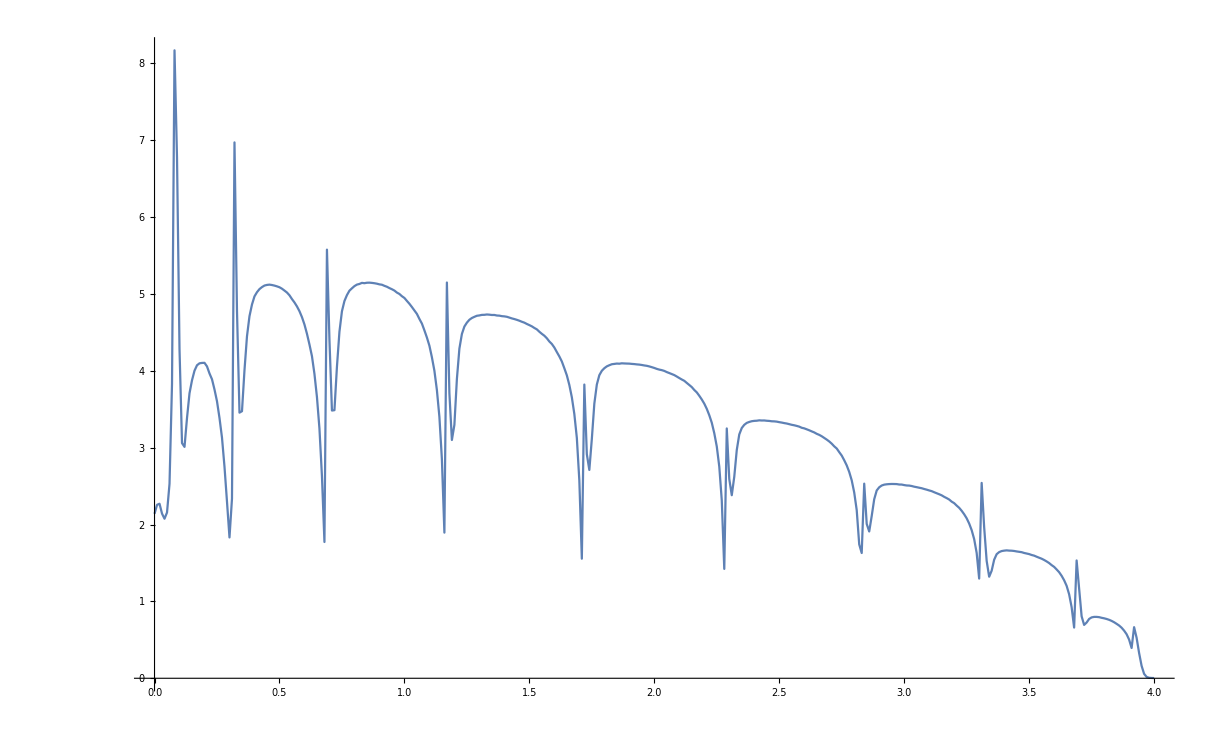

```mathematica
ListPlot[%32,Joined->True]
```

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.4],25000]]},{ω,Range[0,4,0.01]}]
```

{{0.,3.06274},{0.01,3.31476},{0.02,3.27689},{0.03,3.02229},{0.04,2.78298},{0.05,2.55556},{0.06,2.47734},{0.07,3.03947},{0.08,7.66915},{0.09,6.24971},{0.1,3.93766},{0.11,3.89333},{0.12,4.54901},{0.13,4.97382},{0.14,5.18386},{0.15,5.28906},{0.16,5.34643},{0.17,5.38224},{0.18,5.38466},{0.19,5.3786},{0.2,5.3487},{0.21,5.30335},{0.22,5.23244},{0.23,5.13943},{0.24,5.0332},{0.25,4.87269},{0.26,4.67465},{0.27,4.42388},{0.28,4.06861},{0.29,3.51944},{0.3,2.70591},{0.31,2.08768},{0.32,6.66537},{0.33,4.44815},{0.34,4.02935},{0.35,4.84029},{0.36,5.42437},{0.37,5.67951},{0.38,5.79962},{0.39,5.87295},{0.4,5.91787},{0.41,5.95438},{0.42,5.97037},{0.43,5.98234},{0.44,5.9838},{0.45,5.98685},{0.46,5.98322},{0.47,5.97724},{0.48,5.9655},{0.49,5.95503},{0.5,5.9411},{0.51,5.92254},{0.52,5.90315},{0.53,5.87509},{0.54,5.85277},{0.55,5.8047},{0.56,5.76939},{0.57,5.72052},{0.58,5.6636},{0.59,5.58628},{0.6,5.51309},{0.61,5.41596},{0.62,5.30071},{0.63,5.14045},{0.64,4.95583},{0.65,4.69734},{0.66,4.31652},{0.67,3.7043},{0.68,2.5732},{0.69,5.18875},{0.7,4.30506},{0.71,3.80622},{0.72,4.62589},{0.73,5.25051},{0.74,5.49093},{0.75,5.59466},{0.76,5.65655},{0.77,5.68466},{0.78,5.70618},{0.79,5.72391},{0.8,5.73213},{0.81,5.73602},{0.82,5.74483},{0.83,5.74639},{0.84,5.75034},{0.85,5.74229},{0.86,5.73976},{0.87,5.73701},{0.88,5.7328},{0.89,5.72657},{0.9,5.7189},{0.91,5.71573},{0.92,5.70418},{0.93,5.68876},{0.94,5.67616},{0.95,5.66348},{0.96,5.6479},{0.97,5.62797},{0.98,5.61137},{0.99,5.58532},{1.,5.56363},{1.01,5.544},{1.02,5.50742},{1.03,5.47762},{1.04,5.4372},{1.05,5.39804},{1.06,5.34769},{1.07,5.28871},{1.08,5.21875},{1.09,5.14244},{1.1,5.04862},{1.11,4.9264},{1.12,4.76606},{1.13,4.55096},{1.14,4.24201},{1.15,3.72888},{1.16,2.69534},{1.17,5.04608},{1.18,3.6816},{1.19,3.56866},{1.2,4.35171},{1.21,4.83872},{1.22,5.0032},{1.23,5.06943},{1.24,5.1035},{1.25,5.12494},{1.26,5.136},{1.27,5.14655},{1.28,5.15257},{1.29,5.1565},{1.3,5.15978},{1.31,5.16412},{1.32,5.16152},{1.33,5.15956},{1.34,5.15634},{1.35,5.15608},{1.36,5.15395},{1.37,5.14727},{1.38,5.14289},{1.39,5.13985},{1.4,5.13239},{1.41,5.12719},{1.42,5.11794},{1.43,5.11223},{1.44,5.10415},{1.45,5.09615},{1.46,5.08979},{1.47,5.07776},{1.48,5.06514},{1.49,5.0525},{1.5,5.04252},{1.51,5.02796},{1.52,5.00785},{1.53,4.99124},{1.54,4.97101},{1.55,4.95309},{1.56,4.93203},{1.57,4.90357},{1.58,4.87672},{1.59,4.84457},{1.6,4.80932},{1.61,4.76343},{1.62,4.71641},{1.63,4.65669},{1.64,4.59345},{1.65,4.51256},{1.66,4.40253},{1.67,4.27218},{1.68,4.07584},{1.69,3.79713},{1.7,3.2995},{1.71,2.10236},{1.72,3.82999},{1.73,3.01077},{1.74,3.3566},{1.75,3.97475},{1.76,4.23509},{1.77,4.32196},{1.78,4.35994},{1.79,4.38254},{1.8,4.3948},{1.81,4.40308},{1.82,4.41038},{1.83,4.41496},{1.84,4.41476},{1.85,4.41406},{1.86,4.41496},{1.87,4.41493},{1.88,4.41468},{1.89,4.41138},{1.9,4.41028},{1.91,4.40677},{1.92,4.40398},{1.93,4.40042},{1.94,4.39755},{1.95,4.39069},{1.96,4.39012},{1.97,4.38365},{1.98,4.37619},{1.99,4.36898},{2.,4.364},{2.01,4.35713},{2.02,4.34698},{2.03,4.33867},{2.04,4.33152},{2.05,4.32228},{2.06,4.31449},{2.07,4.30119},{2.08,4.28827},{2.09,4.27678},{2.1,4.26337},{2.11,4.24645},{2.12,4.23133},{2.13,4.21512},{2.14,4.19192},{2.15,4.16725},{2.16,4.13916},{2.17,4.11177},{2.18,4.07758},{2.19,4.03851},{2.2,3.99358},{2.21,3.94012},{2.22,3.86973},{2.23,3.79442},{2.24,3.68353},{2.25,3.53348},{2.26,3.30621},{2.27,2.9044},{2.28,1.87952},{2.29,3.28084},{2.3,2.66271},{2.31,2.84969},{2.32,3.28379},{2.33,3.4729},{2.34,3.53558},{2.35,3.55968},{2.36,3.57341},{2.37,3.57953},{2.38,3.58532},{2.39,3.5862},{2.4,3.58653},{2.41,3.58757},{2.42,3.58624},{2.43,3.58418},{2.44,3.5828},{2.45,3.58075},{2.46,3.57709},{2.47,3.57377},{2.48,3.57134},{2.49,3.56926},{2.5,3.56742},{2.51,3.5605},{2.52,3.55446},{2.53,3.55237},{2.54,3.54728},{2.55,3.5396},{2.56,3.53351},{2.57,3.52762},{2.58,3.52116},{2.59,3.51106},{2.6,3.5058},{2.61,3.49684},{2.62,3.48898},{2.63,3.47418},{2.64,3.46582},{2.65,3.45414},{2.66,3.4392},{2.67,3.42699},{2.68,3.40877},{2.69,3.39276},{2.7,3.37468},{2.71,3.35131},{2.72,3.32652},{2.73,3.2976},{2.74,3.2657},{2.75,3.22455},{2.76,3.18147},{2.77,3.12527},{2.78,3.05705},{2.79,2.96439},{2.8,2.83401},{2.81,2.62386},{2.82,2.22171},{2.83,1.49235},{2.84,2.47631},{2.85,2.12357},{2.86,2.31096},{2.87,2.56589},{2.88,2.65291},{2.89,2.68022},{2.9,2.69186},{2.91,2.69712},{2.92,2.70082},{2.93,2.69976},{2.94,2.70113},{2.95,2.7004},{2.96,2.69864},{2.97,2.69678},{2.98,2.69351},{2.99,2.69031},{3.,2.68834},{3.01,2.68337},{3.02,2.68062},{3.03,2.67499},{3.04,2.67158},{3.05,2.66601},{3.06,2.65993},{3.07,2.65232},{3.08,2.64786},{3.09,2.64004},{3.1,2.63186},{3.11,2.62469},{3.12,2.61518},{3.13,2.60522},{3.14,2.59557},{3.15,2.58426},{3.16,2.5701},{3.17,2.55739},{3.18,2.53914},{3.19,2.52309},{3.2,2.50482},{3.21,2.48223},{3.22,2.45524},{3.23,2.42808},{3.24,2.3917},{3.25,2.34774},{3.26,2.29454},{3.27,2.22332},{3.28,2.11604},{3.29,1.96004},{3.3,1.63914},{3.31,2.55229},{3.32,1.9038},{3.33,1.5127},{3.34,1.55444},{3.35,1.70979},{3.36,1.76589},{3.37,1.78005},{3.38,1.78609},{3.39,1.79025},{3.4,1.79036},{3.41,1.78863},{3.42,1.78597},{3.43,1.78268},{3.44,1.77987},{3.45,1.77643},{3.46,1.77157},{3.47,1.76674},{3.48,1.76065},{3.49,1.75447},{3.5,1.74805},{3.51,1.73988},{3.52,1.73196},{3.53,1.72306},{3.54,1.7115},{3.55,1.70086},{3.56,1.68989},{3.57,1.67356},{3.58,1.65948},{3.59,1.64171},{3.6,1.61781},{3.61,1.59332},{3.62,1.56209},{3.63,1.52448},{3.64,1.47873},{3.65,1.41264},{3.66,1.31496},{3.67,1.15096},{3.68,0.756785},{3.69,1.49848},{3.7,0.993562},{3.71,0.773151},{3.72,0.820757},{3.73,0.864273},{3.74,0.874876},{3.75,0.879341},{3.76,0.876335},{3.77,0.874171},{3.78,0.871704},{3.79,0.864552},{3.8,0.859445},{3.81,0.850455},{3.82,0.844086},{3.83,0.829688},{3.84,0.819827},{3.85,0.803454},{3.86,0.781982},{3.87,0.757507},{3.88,0.72618},{3.89,0.681103},{3.9,0.615022},{3.91,0.505646},{3.92,0.549935},{3.93,0.387528},{3.94,0.175826},{3.95,0.0408897},{3.96,0.00845215},{3.97,0.00416303},{3.98,0.0025047},{3.99,0.00182667},{4.,0.00140414}}

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.3],25000]]},{ω,Range[0,4,0.01]}]
```

{{0.,4.82398},{0.01,5.07236},{0.02,4.94518},{0.03,4.65812},{0.04,4.35598},{0.05,3.93237},{0.06,3.37626},{0.07,2.90225},{0.08,6.86899},{0.09,5.58456},{0.1,4.79103},{0.11,5.88239},{0.12,6.34818},{0.13,6.54321},{0.14,6.616},{0.15,6.66532},{0.16,6.68469},{0.17,6.70058},{0.18,6.69847},{0.19,6.66738},{0.2,6.6389},{0.21,6.59745},{0.22,6.54127},{0.23,6.4668},{0.24,6.36945},{0.25,6.25732},{0.26,6.10179},{0.27,5.87987},{0.28,5.56729},{0.29,5.10007},{0.3,4.2833},{0.31,2.74097},{0.32,6.4646},{0.33,4.51617},{0.34,5.61962},{0.35,6.38995},{0.36,6.60133},{0.37,6.68078},{0.38,6.72912},{0.39,6.75646},{0.4,6.77104},{0.41,6.77824},{0.42,6.79155},{0.43,6.78707},{0.44,6.79083},{0.45,6.78749},{0.46,6.77797},{0.47,6.77938},{0.48,6.7675},{0.49,6.76125},{0.5,6.74194},{0.51,6.72907},{0.52,6.71393},{0.53,6.69156},{0.54,6.66704},{0.55,6.64484},{0.56,6.61732},{0.57,6.57652},{0.58,6.53542},{0.59,6.48208},{0.6,6.41932},{0.61,6.34885},{0.62,6.25917},{0.63,6.13852},{0.64,5.99087},{0.65,5.78492},{0.66,5.4747},{0.67,4.95765},{0.68,3.8669},{0.69,4.8038},{0.7,4.27278},{0.71,5.07635},{0.72,5.92481},{0.73,6.12298},{0.74,6.18718},{0.75,6.22086},{0.76,6.24238},{0.77,6.25266},{0.78,6.26128},{0.79,6.26442},{0.8,6.26843},{0.81,6.27098},{0.82,6.27017},{0.83,6.26923},{0.84,6.26802},{0.85,6.26604},{0.86,6.26378},{0.87,6.25832},{0.88,6.25637},{0.89,6.24672},{0.9,6.24415},{0.91,6.2378},{0.92,6.22746},{0.93,6.22165},{0.94,6.21304},{0.95,6.20622},{0.96,6.193},{0.97,6.18004},{0.98,6.16456},{0.99,6.15599},{1.,6.1356},{1.01,6.11795},{1.02,6.09566},{1.03,6.07041},{1.04,6.04658},{1.05,6.01625},{1.06,5.98045},{1.07,5.93711},{1.08,5.88991},{1.09,5.83404},{1.1,5.75823},{1.11,5.66962},{1.12,5.55048},{1.13,5.38742},{1.14,5.13489},{1.15,4.72547},{1.16,3.80464},{1.17,5.03028},{1.18,3.81246},{1.19,4.70946},{1.2,5.31536},{1.21,5.43305},{1.22,5.47368},{1.23,5.49422},{1.24,5.50408},{1.25,5.50988},{1.26,5.51695},{1.27,5.52152},{1.28,5.52172},{1.29,5.52395},{1.3,5.5232},{1.31,5.52074},{1.32,5.51922},{1.33,5.51788},{1.34,5.51614},{1.35,5.51524},{1.36,5.51373},{1.37,5.50732},{1.38,5.50494},{1.39,5.50455},{1.4,5.49944},{1.41,5.4951},{1.42,5.49155},{1.43,5.48381},{1.44,5.47982},{1.45,5.47398},{1.46,5.4674},{1.47,5.45973},{1.48,5.45149},{1.49,5.44411},{1.5,5.436},{1.51,5.42728},{1.52,5.41367},{1.53,5.40385},{1.54,5.38877},{1.55,5.37627},{1.56,5.35597},{1.57,5.34143},{1.58,5.32285},{1.59,5.29863},{1.6,5.27442},{1.61,5.24456},{1.62,5.21247},{1.63,5.17135},{1.64,5.12123},{1.65,5.05844},{1.66,4.98304},{1.67,4.87759},{1.68,4.73796},{1.69,4.5129},{1.7,4.11001},{1.71,2.98295},{1.72,3.84415},{1.73,3.45471},{1.74,4.31456},{1.75,4.56613},{1.76,4.62437},{1.77,4.64714},{1.78,4.65983},{1.79,4.66433},{1.8,4.67018},{1.81,4.67279},{1.82,4.67456},{1.83,4.67529},{1.84,4.67605},{1.85,4.67326},{1.86,4.67302},{1.87,4.67232},{1.88,4.67023},{1.89,4.6689},{1.9,4.66646},{1.91,4.66428},{1.92,4.66252},{1.93,4.66098},{1.94,4.65661},{1.95,4.65329},{1.96,4.65232},{1.97,4.64866},{1.98,4.64483},{1.99,4.63952},{2.,4.63626},{2.01,4.63169},{2.02,4.62532},{2.03,4.62184},{2.04,4.6133},{2.05,4.60975},{2.06,4.60417},{2.07,4.59568},{2.08,4.58671},{2.09,4.58007},{2.1,4.56974},{2.11,4.5596},{2.12,4.54918},{2.13,4.53537},{2.14,4.52277},{2.15,4.50682},{2.16,4.48861},{2.17,4.46866},{2.18,4.44708},{2.19,4.41951},{2.2,4.38695},{2.21,4.34753},{2.22,4.30585},{2.23,4.24247},{2.24,4.16615},{2.25,4.04876},{2.26,3.87408},{2.27,3.54784},{2.28,2.60735},{2.29,3.27898},{2.3,2.98758},{2.31,3.54536},{2.32,3.71221},{2.33,3.74568},{2.34,3.75859},{2.35,3.76713},{2.36,3.77042},{2.37,3.77084},{2.38,3.77269},{2.39,3.77229},{2.4,3.77219},{2.41,3.77132},{2.42,3.77006},{2.43,3.76926},{2.44,3.76813},{2.45,3.76637},{2.46,3.7631},{2.47,3.7607},{2.48,3.75923},{2.49,3.75746},{2.5,3.75543},{2.51,3.75158},{2.52,3.74766},{2.53,3.7452},{2.54,3.74092},{2.55,3.73745},{2.56,3.73469},{2.57,3.72979},{2.58,3.72547},{2.59,3.72036},{2.6,3.71675},{2.61,3.70883},{2.62,3.70482},{2.63,3.69616},{2.64,3.68863},{2.65,3.68294},{2.66,3.67318},{2.67,3.66258},{2.68,3.65454},{2.69,3.641},{2.7,3.63052},{2.71,3.61583},{2.72,3.59916},{2.73,3.58146},{2.74,3.55637},{2.75,3.5301},{2.76,3.49889},{2.77,3.461},{2.78,3.40778},{2.79,3.34047},{2.8,3.23727},{2.81,3.07765},{2.82,2.74304},{2.83,1.47933},{2.84,2.44054},{2.85,2.45456},{2.86,2.75347},{2.87,2.8117},{2.88,2.8267},{2.89,2.8323},{2.9,2.83522},{2.91,2.83669},{2.92,2.83662},{2.93,2.83639},{2.94,2.83573},{2.95,2.83455},{2.96,2.83379},{2.97,2.83192},{2.98,2.82976},{2.99,2.82796},{3.,2.82525},{3.01,2.82346},{3.02,2.8198},{3.03,2.81748},{3.04,2.81408},{3.05,2.81009},{3.06,2.8073},{3.07,2.80393},{3.08,2.80019},{3.09,2.79441},{3.1,2.79036},{3.11,2.78561},{3.12,2.77833},{3.13,2.77291},{3.14,2.76526},{3.15,2.7566},{3.16,2.74982},{3.17,2.74159},{3.18,2.73012},{3.19,2.7177},{3.2,2.70643},{3.21,2.69235},{3.22,2.67239},{3.23,2.65397},{3.24,2.62821},{3.25,2.59685},{3.26,2.55679},{3.27,2.50126},{3.28,2.4244},{3.29,2.29612},{3.3,2.03203},{3.31,2.50162},{3.32,1.79579},{3.33,1.67598},{3.34,1.84109},{3.35,1.87458},{3.36,1.88287},{3.37,1.88584},{3.38,1.88636},{3.39,1.88733},{3.4,1.88629},{3.41,1.88398},{3.42,1.88334},{3.43,1.88031},{3.44,1.87657},{3.45,1.8761},{3.46,1.87196},{3.47,1.86868},{3.48,1.86661},{3.49,1.86193},{3.5,1.857},{3.51,1.85146},{3.52,1.84551},{3.53,1.84246},{3.54,1.83351},{3.55,1.82661},{3.56,1.81973},{3.57,1.80696},{3.58,1.79841},{3.59,1.78519},{3.6,1.77119},{3.61,1.75342},{3.62,1.73282},{3.63,1.70417},{3.64,1.66755},{3.65,1.61733},{3.66,1.54369},{3.67,1.40196},{3.68,0.959994},{3.69,1.35316},{3.7,0.878392},{3.71,0.898628},{3.72,0.930126},{3.73,0.934854},{3.74,0.937006},{3.75,0.935534},{3.76,0.933495},{3.77,0.932003},{3.78,0.927702},{3.79,0.925802},{3.8,0.920866},{3.81,0.91523},{3.82,0.909115},{3.83,0.901838},{3.84,0.893427},{3.85,0.881681},{3.86,0.867837},{3.87,0.852092},{3.88,0.825407},{3.89,0.792877},{3.9,0.739143},{3.91,0.633249},{3.92,0.428428},{3.93,0.205739},{3.94,0.0384518},{3.95,0.00496162},{3.96,0.002337},{3.97,0.0015431},{3.98,0.00109534},{3.99,0.000835733},{4.,0.000650067}}

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.6],25000]]},{ω,Range[0,4,0.01]}]
```

{{0.,1.98627},{0.01,1.98137},{0.02,1.93541},{0.03,1.94658},{0.04,2.10307},{0.05,2.45447},{0.06,3.16067},{0.07,4.79611},{0.08,8.57776},{0.09,7.27556},{0.1,4.90273},{0.11,3.1595},{0.12,2.42477},{0.13,2.30472},{0.14,2.46454},{0.15,2.65524},{0.16,2.76465},{0.17,2.86536},{0.18,2.93014},{0.19,2.94657},{0.2,2.94827},{0.21,2.90841},{0.22,2.85231},{0.23,2.76782},{0.24,2.6448},{0.25,2.49628},{0.26,2.30951},{0.27,2.08069},{0.28,1.82734},{0.29,1.60202},{0.3,1.63095},{0.31,2.97066},{0.32,7.24203},{0.33,5.17627},{0.34,3.56316},{0.35,2.87248},{0.36,2.90229},{0.37,3.23454},{0.38,3.55834},{0.39,3.79418},{0.4,3.93983},{0.41,4.04915},{0.42,4.13526},{0.43,4.17746},{0.44,4.21814},{0.45,4.24013},{0.46,4.25738},{0.47,4.25698},{0.48,4.25821},{0.49,4.24273},{0.5,4.24754},{0.51,4.22726},{0.52,4.20437},{0.53,4.16773},{0.54,4.13425},{0.55,4.08582},{0.56,4.04451},{0.57,3.98874},{0.58,3.9158},{0.59,3.84077},{0.6,3.73801},{0.61,3.61685},{0.62,3.4707},{0.63,3.28763},{0.64,3.05676},{0.65,2.74216},{0.66,2.32594},{0.67,1.80345},{0.68,1.4926},{0.69,5.91174},{0.7,4.67196},{0.71,3.47426},{0.72,2.93353},{0.73,3.02761},{0.74,3.43186},{0.75,3.79349},{0.76,4.0414},{0.77,4.18385},{0.78,4.29156},{0.79,4.35248},{0.8,4.40427},{0.81,4.43431},{0.82,4.46766},{0.83,4.4879},{0.84,4.49473},{0.85,4.50549},{0.86,4.51299},{0.87,4.51549},{0.88,4.51253},{0.89,4.5052},{0.9,4.49744},{0.91,4.49339},{0.92,4.49094},{0.93,4.47622},{0.94,4.45829},{0.95,4.43366},{0.96,4.41361},{0.97,4.39488},{0.98,4.37593},{0.99,4.3435},{1.,4.30309},{1.01,4.27949},{1.02,4.22958},{1.03,4.19469},{1.04,4.13136},{1.05,4.08429},{1.06,4.02352},{1.07,3.94042},{1.08,3.84886},{1.09,3.74034},{1.1,3.61416},{1.11,3.46149},{1.12,3.26086},{1.13,3.00522},{1.14,2.63169},{1.15,2.08285},{1.16,1.44005},{1.17,5.26453},{1.18,3.87831},{1.19,3.01225},{1.2,2.73716},{1.21,2.96064},{1.22,3.37976},{1.23,3.71047},{1.24,3.90815},{1.25,4.03075},{1.26,4.10012},{1.27,4.14528},{1.28,4.18557},{1.29,4.21653},{1.3,4.22639},{1.31,4.23599},{1.32,4.24506},{1.33,4.2506},{1.34,4.25932},{1.35,4.26206},{1.36,4.25907},{1.37,4.25371},{1.38,4.25307},{1.39,4.25048},{1.4,4.23938},{1.41,4.23617},{1.42,4.22656},{1.43,4.21463},{1.44,4.2071},{1.45,4.19674},{1.46,4.18048},{1.47,4.16846},{1.48,4.15338},{1.49,4.13878},{1.5,4.11855},{1.51,4.09482},{1.52,4.07482},{1.53,4.04884},{1.54,4.02186},{1.55,3.98911},{1.56,3.95972},{1.57,3.92407},{1.58,3.88216},{1.59,3.83617},{1.6,3.7891},{1.61,3.72181},{1.62,3.66513},{1.63,3.58456},{1.64,3.49456},{1.65,3.37974},{1.66,3.24323},{1.67,3.06646},{1.68,2.8347},{1.69,2.50328},{1.7,1.94561},{1.71,1.31642},{1.72,3.9018},{1.73,2.98586},{1.74,2.50689},{1.75,2.47355},{1.76,2.79586},{1.77,3.13192},{1.78,3.3683},{1.79,3.50914},{1.8,3.58445},{1.81,3.6359},{1.82,3.66638},{1.83,3.68873},{1.84,3.7069},{1.85,3.71886},{1.86,3.72244},{1.87,3.72977},{1.88,3.73544},{1.89,3.73252},{1.9,3.73181},{1.91,3.73021},{1.92,3.72797},{1.93,3.7265},{1.94,3.72348},{1.95,3.71663},{1.96,3.71189},{1.97,3.70352},{1.98,3.69754},{1.99,3.68687},{2.,3.67936},{2.01,3.66707},{2.02,3.657},{2.03,3.64324},{2.04,3.62653},{2.05,3.61371},{2.06,3.59682},{2.07,3.58257},{2.08,3.56378},{2.09,3.544},{2.1,3.52313},{2.11,3.50156},{2.12,3.47665},{2.13,3.44951},{2.14,3.41427},{2.15,3.38095},{2.16,3.34544},{2.17,3.30006},{2.18,3.24811},{2.19,3.19415},{2.2,3.13366},{2.21,3.05692},{2.22,2.97073},{2.23,2.85386},{2.24,2.71517},{2.25,2.52622},{2.26,2.24108},{2.27,1.79117},{2.28,1.22048},{2.29,3.33313},{2.3,2.63571},{2.31,2.20806},{2.32,2.13045},{2.33,2.34773},{2.34,2.61173},{2.35,2.81641},{2.36,2.9238},{2.37,2.9892},{2.38,3.02416},{2.39,3.04314},{2.4,3.05648},{2.41,3.07047},{2.42,3.07177},{2.43,3.07894},{2.44,3.07816},{2.45,3.07767},{2.46,3.07619},{2.47,3.07508},{2.48,3.06929},{2.49,3.06598},{2.5,3.0625},{2.51,3.05609},{2.52,3.04628},{2.53,3.04241},{2.54,3.03177},{2.55,3.02928},{2.56,3.01503},{2.57,3.00511},{2.58,2.99106},{2.59,2.98162},{2.6,2.97103},{2.61,2.96065},{2.62,2.94344},{2.63,2.92522},{2.64,2.90871},{2.65,2.8899},{2.66,2.86796},{2.67,2.84548},{2.68,2.82269},{2.69,2.79591},{2.7,2.76987},{2.71,2.73437},{2.72,2.69948},{2.73,2.65945},{2.74,2.61125},{2.75,2.55602},{2.76,2.49082},{2.77,2.41769},{2.78,2.31926},{2.79,2.19647},{2.8,2.0276},{2.81,1.77609},{2.82,1.34354},{2.83,1.78137},{2.84,2.56385},{2.85,2.06322},{2.86,1.75033},{2.87,1.70992},{2.88,1.87276},{2.89,2.05722},{2.9,2.17888},{2.91,2.2487},{2.92,2.2798},{2.93,2.30048},{2.94,2.31264},{2.95,2.31546},{2.96,2.32178},{2.97,2.3202},{2.98,2.31874},{2.99,2.31904},{3.,2.31314},{3.01,2.31086},{3.02,2.30299},{3.03,2.29741},{3.04,2.28782},{3.05,2.28395},{3.06,2.27423},{3.07,2.2641},{3.08,2.25502},{3.09,2.24006},{3.1,2.23245},{3.11,2.21715},{3.12,2.20553},{3.13,2.18806},{3.14,2.17168},{3.15,2.15519},{3.16,2.13202},{3.17,2.11647},{3.18,2.09094},{3.19,2.06037},{3.2,2.03239},{3.21,2.0021},{3.22,1.96566},{3.23,1.92256},{3.24,1.86856},{3.25,1.81302},{3.26,1.73652},{3.27,1.64215},{3.28,1.51104},{3.29,1.32717},{3.3,1.01576},{3.31,2.51651},{3.32,2.05821},{3.33,1.59304},{3.34,1.28371},{3.35,1.16463},{3.36,1.23527},{3.37,1.34531},{3.38,1.42991},{3.39,1.46862},{3.4,1.49362},{3.41,1.50202},{3.42,1.5059},{3.43,1.50583},{3.44,1.50614},{3.45,1.50256},{3.46,1.49699},{3.47,1.48818},{3.48,1.48205},{3.49,1.47041},{3.5,1.46211},{3.51,1.4503},{3.52,1.43709},{3.53,1.42468},{3.54,1.41009},{3.55,1.39072},{3.56,1.36981},{3.57,1.34818},{3.58,1.3256},{3.59,1.30097},{3.6,1.27048},{3.61,1.23201},{3.62,1.19403},{3.63,1.13798},{3.64,1.0816},{3.65,0.99827},{3.66,0.891165},{3.67,0.732449},{3.68,0.630684},{3.69,1.62741},{3.7,1.25439},{3.71,0.94104},{3.72,0.69641},{3.73,0.602626},{3.74,0.619397},{3.75,0.659103},{3.76,0.684898},{3.77,0.696829},{3.78,0.695156},{3.79,0.693612},{3.8,0.690395},{3.81,0.680105},{3.82,0.666105},{3.83,0.651743},{3.84,0.633403},{3.85,0.612331},{3.86,0.588151},{3.87,0.552082},{3.88,0.510621},{3.89,0.467918},{3.9,0.405123},{3.91,0.319143},{3.92,0.758358},{3.93,0.666783},{3.94,0.480949},{3.95,0.303954},{3.96,0.163577},{3.97,0.0706873},{3.98,0.0280577},{3.99,0.011805},{4.,0.0056016}}

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.7],25000]]},{ω,Range[0,4,0.01]}]
```

{{0.,2.28216},{0.01,2.24495},{0.02,2.17333},{0.03,2.27085},{0.04,2.53405},{0.05,3.01746},{0.06,3.9183},{0.07,5.6369},{0.08,8.84222},{0.09,7.58766},{0.1,5.4958},{0.11,3.71379},{0.12,2.5364},{0.13,1.95785},{0.14,1.7842},{0.15,1.80648},{0.16,1.86418},{0.17,1.92437},{0.18,1.97569},{0.19,2.00325},{0.2,2.00603},{0.21,1.9896},{0.22,1.93714},{0.23,1.87263},{0.24,1.78272},{0.25,1.67178},{0.26,1.56909},{0.27,1.45268},{0.28,1.36843},{0.29,1.4359},{0.3,1.92501},{0.31,3.72883},{0.32,7.43232},{0.33,5.52886},{0.34,3.89908},{0.35,2.78776},{0.36,2.40079},{0.37,2.37851},{0.38,2.57036},{0.39,2.77542},{0.4,2.97396},{0.41,3.11636},{0.42,3.23223},{0.43,3.30663},{0.44,3.36644},{0.45,3.4036},{0.46,3.42982},{0.47,3.43756},{0.48,3.44767},{0.49,3.46498},{0.5,3.43214},{0.51,3.43257},{0.52,3.40789},{0.53,3.37579},{0.54,3.34211},{0.55,3.30358},{0.56,3.25982},{0.57,3.20476},{0.58,3.13586},{0.59,3.048},{0.6,2.93407},{0.61,2.81901},{0.62,2.65241},{0.63,2.49489},{0.64,2.25048},{0.65,1.95995},{0.66,1.63396},{0.67,1.32757},{0.68,1.59743},{0.69,6.23833},{0.7,4.92237},{0.71,3.58924},{0.72,2.80388},{0.73,2.54019},{0.74,2.61725},{0.75,2.86196},{0.76,3.13714},{0.77,3.34908},{0.78,3.49711},{0.79,3.60159},{0.8,3.6859},{0.81,3.73545},{0.82,3.782},{0.83,3.81395},{0.84,3.8414},{0.85,3.854},{0.86,3.86952},{0.87,3.88544},{0.88,3.88169},{0.89,3.87975},{0.9,3.87821},{0.91,3.8821},{0.92,3.88077},{0.93,3.86387},{0.94,3.84336},{0.95,3.82244},{0.96,3.81407},{0.97,3.79784},{0.98,3.75248},{0.99,3.73406},{1.,3.70701},{1.01,3.65802},{1.02,3.6152},{1.03,3.56611},{1.04,3.51127},{1.05,3.45036},{1.06,3.38005},{1.07,3.311},{1.08,3.21756},{1.09,3.10142},{1.1,2.9707},{1.11,2.81241},{1.12,2.60194},{1.13,2.32864},{1.14,1.9665},{1.15,1.49418},{1.16,1.27994},{1.17,5.37295},{1.18,3.99732},{1.19,3.05495},{1.2,2.52944},{1.21,2.40852},{1.22,2.57932},{1.23,2.88917},{1.24,3.15774},{1.25,3.35013},{1.26,3.47215},{1.27,3.5571},{1.28,3.62182},{1.29,3.66328},{1.3,3.69677},{1.31,3.71958},{1.32,3.73906},{1.33,3.75895},{1.34,3.75275},{1.35,3.75996},{1.36,3.766},{1.37,3.76468},{1.38,3.7667},{1.39,3.76413},{1.4,3.75896},{1.41,3.75638},{1.42,3.75531},{1.43,3.74096},{1.44,3.7303},{1.45,3.71922},{1.46,3.70574},{1.47,3.69224},{1.48,3.68739},{1.49,3.65615},{1.5,3.64024},{1.51,3.61751},{1.52,3.59124},{1.53,3.56836},{1.54,3.53629},{1.55,3.50687},{1.56,3.46928},{1.57,3.42909},{1.58,3.38557},{1.59,3.3356},{1.6,3.28593},{1.61,3.21968},{1.62,3.14337},{1.63,3.07301},{1.64,2.96688},{1.65,2.84574},{1.66,2.71307},{1.67,2.53091},{1.68,2.27358},{1.69,1.94031},{1.7,1.44392},{1.71,1.29602},{1.72,3.96995},{1.73,3.06555},{1.74,2.47513},{1.75,2.17811},{1.76,2.22219},{1.77,2.4365},{1.78,2.69598},{1.79,2.91134},{1.8,3.05359},{1.81,3.14172},{1.82,3.20945},{1.83,3.25391},{1.84,3.28045},{1.85,3.30297},{1.86,3.31719},{1.87,3.32715},{1.88,3.33661},{1.89,3.33763},{1.9,3.34642},{1.91,3.34206},{1.92,3.34711},{1.93,3.34452},{1.94,3.34769},{1.95,3.33316},{1.96,3.33249},{1.97,3.32441},{1.98,3.31641},{1.99,3.30607},{2.,3.29889},{2.01,3.28841},{2.02,3.27764},{2.03,3.26597},{2.04,3.24982},{2.05,3.23198},{2.06,3.21815},{2.07,3.19818},{2.08,3.17984},{2.09,3.1588},{2.1,3.13804},{2.11,3.10462},{2.12,3.08058},{2.13,3.05007},{2.14,3.01723},{2.15,2.97735},{2.16,2.9434},{2.17,2.89096},{2.18,2.84106},{2.19,2.78712},{2.2,2.71554},{2.21,2.62919},{2.22,2.53431},{2.23,2.40957},{2.24,2.26262},{2.25,2.07195},{2.26,1.7805},{2.27,1.34996},{2.28,1.18205},{2.29,3.35233},{2.3,2.68956},{2.31,2.19848},{2.32,1.92813},{2.33,1.92004},{2.34,2.06996},{2.35,2.26293},{2.36,2.42837},{2.37,2.56103},{2.38,2.63933},{2.39,2.68967},{2.4,2.71747},{2.41,2.73841},{2.42,2.75683},{2.43,2.76757},{2.44,2.77112},{2.45,2.77985},{2.46,2.77909},{2.47,2.7757},{2.48,2.77636},{2.49,2.773},{2.5,2.76876},{2.51,2.76047},{2.52,2.75797},{2.53,2.74982},{2.54,2.74477},{2.55,2.73298},{2.56,2.72339},{2.57,2.71432},{2.58,2.69917},{2.59,2.68676},{2.6,2.67059},{2.61,2.6567},{2.62,2.64882},{2.63,2.62397},{2.64,2.60838},{2.65,2.58696},{2.66,2.56217},{2.67,2.53878},{2.68,2.51373},{2.69,2.48313},{2.7,2.44707},{2.71,2.41704},{2.72,2.37673},{2.73,2.33292},{2.74,2.28303},{2.75,2.2231},{2.76,2.15493},{2.77,2.07554},{2.78,1.96908},{2.79,1.84317},{2.8,1.66778},{2.81,1.40729},{2.82,1.04704},{2.83,1.91624},{2.84,2.57087},{2.85,2.08459},{2.86,1.75085},{2.87,1.53659},{2.88,1.53787},{2.89,1.63101},{2.9,1.77335},{2.91,1.89631},{2.92,1.97639},{2.93,2.02013},{2.94,2.05009},{2.95,2.0686},{2.96,2.07984},{2.97,2.08741},{2.98,2.08957},{2.99,2.09096},{3.,2.08947},{3.01,2.0872},{3.02,2.07804},{3.03,2.07434},{3.04,2.06752},{3.05,2.05494},{3.06,2.05391},{3.07,2.04341},{3.08,2.02985},{3.09,2.01935},{3.1,2.00165},{3.11,1.98844},{3.12,1.97088},{3.13,1.95564},{3.14,1.94333},{3.15,1.92124},{3.16,1.89712},{3.17,1.87504},{3.18,1.84622},{3.19,1.8203},{3.2,1.78981},{3.21,1.7518},{3.22,1.70718},{3.23,1.66768},{3.24,1.61044},{3.25,1.54731},{3.26,1.46399},{3.27,1.37608},{3.28,1.23571},{3.29,1.04822},{3.3,0.807827},{3.31,2.5254},{3.32,2.08263},{3.33,1.74433},{3.34,1.33992},{3.35,1.1022},{3.36,1.02479},{3.37,1.06433},{3.38,1.14493},{3.39,1.22183},{3.4,1.27139},{3.41,1.30449},{3.42,1.3208},{3.43,1.32608},{3.44,1.33608},{3.45,1.33199},{3.46,1.32792},{3.47,1.32372},{3.48,1.31171},{3.49,1.30925},{3.5,1.29891},{3.51,1.28203},{3.52,1.27168},{3.53,1.25349},{3.54,1.24161},{3.55,1.22167},{3.56,1.20064},{3.57,1.17451},{3.58,1.15225},{3.59,1.12504},{3.6,1.09153},{3.61,1.0556},{3.62,1.01115},{3.63,0.956676},{3.64,0.893096},{3.65,0.814724},{3.66,0.715051},{3.67,0.587176},{3.68,0.654526},{3.69,1.68238},{3.7,1.36913},{3.71,1.09772},{3.72,0.812724},{3.73,0.62645},{3.74,0.547647},{3.75,0.52703},{3.76,0.538283},{3.77,0.562573},{3.78,0.579129},{3.79,0.581463},{3.8,0.579533},{3.81,0.576574},{3.82,0.559309},{3.83,0.548487},{3.84,0.52862},{3.85,0.509216},{3.86,0.484005},{3.87,0.454295},{3.88,0.417441},{3.89,0.376371},{3.9,0.326847},{3.91,0.274194},{3.92,0.834711},{3.93,0.763782},{3.94,0.603802},{3.95,0.448086},{3.96,0.306483},{3.97,0.168181},{3.98,0.0914452},{3.99,0.0483954},{4.,0.0197796}}

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.8],25000]]},{ω,Range[0,4,0.01]}]
```

{{0.,2.81799},{0.01,2.72026},{0.02,2.65206},{0.03,2.77137},{0.04,3.13488},{0.05,3.71892},{0.06,4.64865},{0.07,6.33057},{0.08,9.02688},{0.09,7.81195},{0.1,5.94382},{0.11,4.25567},{0.12,2.96696},{0.13,2.15694},{0.14,1.7264},{0.15,1.50976},{0.16,1.43384},{0.17,1.40014},{0.18,1.39},{0.19,1.4094},{0.2,1.38127},{0.21,1.38384},{0.22,1.34553},{0.23,1.3199},{0.24,1.28549},{0.25,1.24771},{0.26,1.23524},{0.27,1.24396},{0.28,1.33887},{0.29,1.64905},{0.3,2.40771},{0.31,4.4479},{0.32,7.62929},{0.33,5.79555},{0.34,4.21602},{0.35,3.06443},{0.36,2.35819},{0.37,2.00597},{0.38,1.94068},{0.39,2.0347},{0.4,2.16335},{0.41,2.29344},{0.42,2.4147},{0.43,2.495},{0.44,2.58435},{0.45,2.63245},{0.46,2.66917},{0.47,2.70069},{0.48,2.70676},{0.49,2.72971},{0.5,2.70576},{0.51,2.71076},{0.52,2.69519},{0.53,2.66122},{0.54,2.63083},{0.55,2.59791},{0.56,2.5443},{0.57,2.49898},{0.58,2.42088},{0.59,2.33592},{0.6,2.22186},{0.61,2.12051},{0.62,1.96797},{0.63,1.80696},{0.64,1.60594},{0.65,1.40389},{0.66,1.21302},{0.67,1.20307},{0.68,1.93212},{0.69,6.54238},{0.7,5.04435},{0.71,3.83364},{0.72,2.85484},{0.73,2.3685},{0.74,2.17235},{0.75,2.2216},{0.76,2.36812},{0.77,2.55808},{0.78,2.72633},{0.79,2.86433},{0.8,2.97377},{0.81,3.05114},{0.82,3.1186},{0.83,3.15874},{0.84,3.20018},{0.85,3.23333},{0.86,3.25324},{0.87,3.26434},{0.88,3.27572},{0.89,3.28702},{0.9,3.28816},{0.91,3.29111},{0.92,3.28543},{0.93,3.27441},{0.94,3.27012},{0.95,3.25028},{0.96,3.22789},{0.97,3.21173},{0.98,3.1873},{0.99,3.16699},{1.,3.13029},{1.01,3.08723},{1.02,3.04086},{1.03,2.99075},{1.04,2.93406},{1.05,2.86998},{1.06,2.79156},{1.07,2.72432},{1.08,2.62317},{1.09,2.51651},{1.1,2.3821},{1.11,2.21038},{1.12,2.00609},{1.13,1.74206},{1.14,1.4281},{1.15,1.13922},{1.16,1.37713},{1.17,5.5087},{1.18,4.16513},{1.19,3.21},{1.2,2.54366},{1.21,2.17263},{1.22,2.12193},{1.23,2.25074},{1.24,2.44266},{1.25,2.633},{1.26,2.81104},{1.27,2.93441},{1.28,3.02858},{1.29,3.09498},{1.3,3.1519},{1.31,3.19109},{1.32,3.22172},{1.33,3.24658},{1.34,3.2559},{1.35,3.27074},{1.36,3.27611},{1.37,3.27743},{1.38,3.28434},{1.39,3.29262},{1.4,3.28863},{1.41,3.28531},{1.42,3.28097},{1.43,3.26889},{1.44,3.26169},{1.45,3.25588},{1.46,3.23805},{1.47,3.23333},{1.48,3.21406},{1.49,3.19787},{1.5,3.17324},{1.51,3.15889},{1.52,3.13474},{1.53,3.09504},{1.54,3.07551},{1.55,3.04287},{1.56,2.99819},{1.57,2.96038},{1.58,2.91589},{1.59,2.85965},{1.6,2.81139},{1.61,2.74428},{1.62,2.67202},{1.63,2.59969},{1.64,2.48103},{1.65,2.3669},{1.66,2.21937},{1.67,2.03106},{1.68,1.77228},{1.69,1.46395},{1.7,1.11135},{1.71,1.41659},{1.72,4.05592},{1.73,3.14573},{1.74,2.45809},{1.75,2.10617},{1.76,1.92905},{1.77,1.95104},{1.78,2.1137},{1.79,2.29669},{1.8,2.47802},{1.81,2.59889},{1.82,2.70643},{1.83,2.77605},{1.84,2.83572},{1.85,2.86373},{1.86,2.89372},{1.87,2.909},{1.88,2.92906},{1.89,2.93877},{1.9,2.94565},{1.91,2.9526},{1.92,2.95432},{1.93,2.95454},{1.94,2.95021},{1.95,2.9455},{1.96,2.94688},{1.97,2.94039},{1.98,2.93674},{1.99,2.92756},{2.,2.92141},{2.01,2.90681},{2.02,2.89841},{2.03,2.8868},{2.04,2.86987},{2.05,2.85236},{2.06,2.84225},{2.07,2.81735},{2.08,2.79681},{2.09,2.77837},{2.1,2.75432},{2.11,2.72469},{2.12,2.69773},{2.13,2.67197},{2.14,2.62663},{2.15,2.59008},{2.16,2.54582},{2.17,2.50021},{2.18,2.44863},{2.19,2.37603},{2.2,2.31027},{2.21,2.21949},{2.22,2.12277},{2.23,2.00467},{2.24,1.84634},{2.25,1.6469},{2.26,1.3774},{2.27,1.03505},{2.28,1.25187},{2.29,3.40547},{2.3,2.72143},{2.31,2.24301},{2.32,1.86702},{2.33,1.6977},{2.34,1.68693},{2.35,1.77229},{2.36,1.91622},{2.37,2.06213},{2.38,2.18031},{2.39,2.27376},{2.4,2.334},{2.41,2.37409},{2.42,2.4041},{2.43,2.42379},{2.44,2.44296},{2.45,2.45109},{2.46,2.46077},{2.47,2.4594},{2.48,2.47016},{2.49,2.46754},{2.5,2.46496},{2.51,2.45907},{2.52,2.45162},{2.53,2.44715},{2.54,2.44069},{2.55,2.43193},{2.56,2.42366},{2.57,2.41332},{2.58,2.39768},{2.59,2.38652},{2.6,2.37306},{2.61,2.36204},{2.62,2.34246},{2.63,2.32498},{2.64,2.30169},{2.65,2.2798},{2.66,2.25827},{2.67,2.22649},{2.68,2.20508},{2.69,2.17832},{2.7,2.13902},{2.71,2.10886},{2.72,2.06149},{2.73,2.01361},{2.74,1.96016},{2.75,1.9054},{2.76,1.82934},{2.77,1.74585},{2.78,1.63721},{2.79,1.50747},{2.8,1.33651},{2.81,1.08954},{2.82,0.854016},{2.83,2.07821},{2.84,2.67297},{2.85,2.17125},{2.86,1.79398},{2.87,1.50245},{2.88,1.35823},{2.89,1.32971},{2.9,1.39208},{2.91,1.49664},{2.92,1.60655},{2.93,1.68499},{2.94,1.74166},{2.95,1.78746},{2.96,1.81229},{2.97,1.8272},{2.98,1.83224},{2.99,1.84207},{3.,1.84544},{3.01,1.84207},{3.02,1.84035},{3.03,1.83555},{3.04,1.83334},{3.05,1.82662},{3.06,1.81405},{3.07,1.80451},{3.08,1.79698},{3.09,1.78303},{3.1,1.773},{3.11,1.76038},{3.12,1.73906},{3.13,1.72766},{3.14,1.70218},{3.15,1.68698},{3.16,1.65948},{3.17,1.63966},{3.18,1.61253},{3.19,1.57958},{3.2,1.5488},{3.21,1.50721},{3.22,1.46608},{3.23,1.42169},{3.24,1.3658},{3.25,1.29571},{3.26,1.21783},{3.27,1.11979},{3.28,0.987662},{3.29,0.826102},{3.3,0.688322},{3.31,2.57339},{3.32,2.18357},{3.33,1.78785},{3.34,1.4758},{3.35,1.16761},{3.36,1.00526},{3.37,0.912047},{3.38,0.903726},{3.39,0.96261},{3.4,1.01864},{3.41,1.06576},{3.42,1.10771},{3.43,1.12124},{3.44,1.137},{3.45,1.14318},{3.46,1.1448},{3.47,1.14463},{3.48,1.13832},{3.49,1.13203},{3.5,1.12075},{3.51,1.11256},{3.52,1.10248},{3.53,1.08265},{3.54,1.06822},{3.55,1.04861},{3.56,1.0291},{3.57,1.00393},{3.58,0.977898},{3.59,0.948431},{3.6,0.91305},{3.61,0.881121},{3.62,0.832379},{3.63,0.785752},{3.64,0.724641},{3.65,0.651787},{3.66,0.572232},{3.67,0.494234},{3.68,0.694817},{3.69,1.75223},{3.7,1.47979},{3.71,1.18952},{3.72,0.956045},{3.73,0.738343},{3.74,0.570667},{3.75,0.487518},{3.76,0.442459},{3.77,0.439151},{3.78,0.449874},{3.79,0.458644},{3.8,0.461773},{3.81,0.462765},{3.82,0.453184},{3.83,0.444491},{3.84,0.429805},{3.85,0.410499},{3.86,0.386906},{3.87,0.362692},{3.88,0.334067},{3.89,0.302389},{3.9,0.271837},{3.91,0.257251},{3.92,0.896928},{3.93,0.838869},{3.94,0.720393},{3.95,0.572289},{3.96,0.438541},{3.97,0.314045},{3.98,0.194476},{3.99,0.131532},{4.,0.0744793}}

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.9],25000]]},{ω,Range[0,4,0.01]}]
```